```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yinshi/Documents/work/post-doc-Humboldt/github/Moat-meanfield/MF_DR/yukawa

# F1B1

```mathematica
F1B1[mf2_,mb2_]:=1/2(-nb[Eb[mb2]]/Eb[mb2]*1/((ⅈ p0-mu+Eb[mb2])^2-Eq[mf2]^2)
-(nb[Eb[mb2]]+1)/Eb[mb2]*1/((ⅈ p0-mu-Eb[mb2])^2-Eq[mf2]^2)
+nfa[Eq[mf2]]/Eq[mf2]*1/((ⅈ p0-mu-Eq[mf2])^2-Eb[mb2]^2)
+(nff[Eq[mf2]]-1)/Eq[mf2]*1/((ⅈ p0-mu+Eq[mf2])^2-Eb[mb2]^2));
```

```mathematica
1/2(-1/Eb[mb2]*1/((ⅈ p0-mu-Eb[mb2])^2-Eq[mf2]^2)
-1/Eq[mf2]*1/((ⅈ p0-mu+Eq[mf2])^2-Eb[mb2]^2))/.{mu->0,p0->π T}//Simplify
```

(Eb[mb2]+Eq[mf2])/(2 Eb[mb2] Eq[mf2] (π^2 T^2+Eb[mb2]^2+2 Eb[mb2] Eq[mf2]+Eq[mf2]^2))

# Equation of Yukawa coupling

We can compute the quark propagator with one-loop correction. Here we only consider the correction from Pion.
So the loop function can be written as
h^2 C_2(N_f)(-ⅈq_μ γ_μ-m_f)G_q(q)G_π(q-p)
Then we perform the projection
Z_q=1/p^2 1/4 tr[(OverVector[ip]γ⃗)  h^2 C_2(N_f)(-ⅈq_μ γ_μ-m_f)G_q(q)G_π(q-p)]
=1/p^2 p⃗ q⃗ cosθ h^2 C_2(N_f)G_q(q)G_π(q-p)
To compute the wave function renormalization of quark at vanishing spatial momentum, we can expand the pion propagator at p⃗=0
G_π(q-p)=1/((Z_0(q_0-p_0))^2+(Z_s(q⃗-p⃗))^2+m_π^2)
=1/((q_0-p_0)^2+(Z_s(q⃗-p⃗))^2+m_π^2)
=1/((q_0-p_0)^2+Z_s(q⃗)^2+m_π^2)-((q⃗-p⃗)^2-(q⃗)^2)/(((q_0-p_0)^2+Z_s(q⃗)^2+m_π^2)^2)+(((q⃗-p⃗)^2-(q⃗)^2)^2)/(((q_0-p_0)^2+Z_s(q⃗)^2+m_π^2)^3)
=G_π(q_0-p_0)-((q⃗-p⃗)^2-(q⃗)^2)G_π^2(q_0-p_0)+((q⃗-p⃗)^2-(q⃗)^2)^2 G_π^3(q_0-p_0)
=G_π(q_0-p_0)-((p⃗)^2-2 q⃗ p⃗ cosθ)G_π^2(q_0-p_0)+((p⃗)^4+4(q⃗)^2 (p⃗)^2 cos^2 θ-4 q⃗ (p⃗)^3 cosθ)G_π^3(q_0-p_0)  Here we set Z_0=1
Here we keep the (p⃗)^1terms
=2 q⃗ p⃗ cosθ G_π^2(q_0-p_0)
then we have
Z_q=1/p^2 p⃗ q⃗ cosθ h^2 C_2(N_f)G_q(q)2 q⃗ p⃗ cosθ G_π^2(q_0-p_0)
=2 h^2 C_2(N_f)(q⃗)^2 cos^2 θ G_q(q)G_π^2(q_0-p_0)
Then perform the Matsubara Summation and loop momentum integral
=2 h^2 C_2(N_f)1/(2π)^2 TΣ_n∫q^2 dq(∫_-1)^1 dcosθ (q⃗)^2 cos^2 θ G_q(q)G_π^2(q_0-p_0)
=1/(3 π^2)h^2 C_2(N_f)∫dq q^4 F1B2

# Equation of Z_q p^2

We can compute the quark propagator with one-loop correction. Here we only consider the correction from Pion.
So the loop function can be written as
h^2 C_2(N_f)(-ⅈq_μ γ_μ-m_f)G_q(q)G_π(q-p)
Then we perform the projection
Z_q(p)p^2=1/4 tr[(OverVector[ip]γ⃗)  h^2 C_2(N_f)(-ⅈq_μ γ_μ-m_f)G_q(q)G_π(q-p)]
=p⃗ q⃗ cosθ h^2 C_2(N_f)G_q(q)G_π(q-p)
Then perform the Matsubara Summation and loop momentum integral
=(h^2 C_2(N_f))/(4 π^2)∫dq q^2 dcosθ p⃗ q⃗ cosθ FB_(1,1)(p)

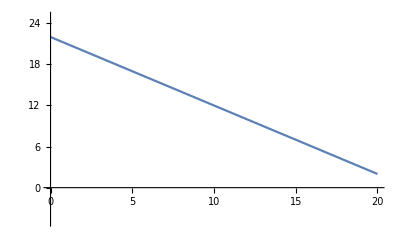

```mathematica
Plot[√(q^2+p^2-2p q x)/.{x->1,p->22},{q,0,20},PlotRange->{{0,20},{-5,25}}]
```

# Equation of m_f

We can compute the quark propagator with one-loop correction. Here we only consider the correction from Pion.
So the loop function can be written as
h^2 C_2(N_f)(-ⅈq_μ γ_μ-m_f)G_q(q)G_π(q-p)
Then we perform the projection
m_f(p)=1/4 tr[h^2 C_2(N_f)(-ⅈq_μ γ_μ-m_f)G_q(q)G_π(q-p)]
= h^2 C_2(N_f)m_f G_q(q)G_π(q-p)
Then perform the Matsubara Summation and loop momentum integral
=(h^2 C_2(N_f))/(4 π^2)m_f∫dq q^2 dcosθ  FB_(1,1)(p)

# Equation of Z_q p_0

We can compute the quark propagator with one-loop correction. Here we only consider the correction from Pion.
So the loop function can be written as
h^2 C_2(N_f)(-ⅈq_μ γ_μ-m_f)G_q(q)G_π(q-p)
Then we perform the projection
Z_q(p)(p_0+μ)=1/(4(-ⅈ))tr[γ_0 h^2 C_2(N_f)(-ⅈq_μ γ_μ-m_f)G_q(q)G_π(q-p)]
 =h^2 C_2(N_f)1/(4(-ⅈ))tr[(-ⅈq_0 γ_0 γ_0)G_q(q)G_π(q-p)] 
=h^2 C_2(N_f)q_0 G_q(q)G_π(q-p)
Then perform the Matsubara Summation and loop momentum integral
=(h^2 C_2(N_f))/(4 π^2)∫dq q^2 dcosθ  FBq0_(1,1)(p)